# General Systems of Haken-Kelso-Bunz (HKB) Oscillators

## Introduction

The Haken-Kelso-Bunz model arises as an approximation to a system of N + 1 hybrid Rayleigh-van-der-Pol oscillators, with the dynamics of the ith-oscillator given by

(x^(..))_i - (α_i - β_i((ẋ)^2)_i - γ_i(x^2)_i )(ẋ)_i + (ω^2)_i x_i = -∑_(j=0)^N [a_ij - b_ij((ẋ)_i-(ẋ)_j)^2 - c_ij(x_i-x_j)^2]((ẋ)_i-(ẋ)_j)

where x_i(t) is the position of the ith oscillator, for i = 0, ..., N, and each oscillator’s internal parameters (α_i, β_i, γ_i, ω_i) and coupling parameters (a_ij, b_ij, c_ij) are all positive.  

For small velocities (β_i((ẋ)_i)^2 <<α_i) and amplitudes (γ_i x_i^2 << α_i),  each oscillator in isolation exhibits self-excitatory oscillations that are nearly harmonic with frequency ω_i ~ Ω  and amplitude r_i ~ (4 α_i)/(3 β_i Ω^2 + γ_i) .  

However, the coupling terms permit other stable, collective motions where the oscillators deviate away from their preferred, autonomous motions, and coordinate to form complex behaviors.  HKB aims to classify and understand these coordination states.


The HKB model emerges through a sequence of approximations, which reduce the Rayleigh-van-der-Pol equations from an N+1-dimensional system to an N-dimensional system.  This is the key aim of synergetics: to obtain a simpler, lower dimensional description of a complex system by introduction of order parameters which characterize the coordination dynamics of the system.

First, we recast each oscillator’s position in terms of its amplitude and phase as

x_i(t) =: r_i(t)cos(Ωt+θ_i(t))                 and                (ẋ)_i(t) =: -Ωr_i(t)sin(Ωt+θ_i(t))

where Ω is a collective frequency to which the oscillators become entrained that is a function of the system parameters.

Next, one restricts to motions where each oscillator’s anomalous phase θ_i(t) varies slowly over a period T = (2π)/Ω.

Finally, one replaces equation (1) with its average over a single period T (a Krylov-Bogliubov approximation), which gives the HKB anomalous phase equations

(θ̇)_i(t) = (ω_i^2-Ω^2)/(2Ω) - ∑_(j!=i) [A_ij sin(θ_i-θ_j) - 2 B_ij sin2(θ_i-θ_j)]

where the effective coupling parameters are

A_ij(t) := a_ij/2(r_j(t))/(r_i(t)) -  2(r_i(t)^2+r_j(t)^2)/(r_i(t)r_j(t))B_ij(t)                             with                              B_ij(t) := (3 b_ij Ω^2+c_ij)/16 r_j(t)^2

and the amplitude equations are given by

((ṙ)_i(t))/(r_i(t)) = OverTilde[α_i]/2 - (3(β̃)_i Ω^2+(γ̃)_i)/8 r_i^2 + ∑_(j!=i) [4 B_ij + (A_ij r_j-4 B_ij r_i)/r_j cos(θ_i-θ_j) + 2 B_ij cos2(θ_i-θ_j)]

where the amplitude-independent modified internal parameters are

(α̃)_i : = α_i - ∑_(j≠i) a_ij,                         (β̃)_i := β_i - ∑_(j≠i) b_ij,                          and          (γ̃)_i := γ_i - ∑_(j≠i) c_ij.

One final approximation we make is assuming that the amplitudes are approximately constant in time.  We will explore the dynamics for when this slowly-varying amplitude approximation is not applied and compare them, as there is much research investigating the experimental effects of variable amplitudes in pairs of HKB oscillators.  Invoking this approximation leaves us with equation (3), the generalized HKB absolute phase equations.


Now we are ready to derive the original HKB model.  It can be shown that stationary states of the HKB anomalous phase equations include motions where the different oscillators move rhythmically in combinations of in-phase and anti-phase motions.  Hence, the coordination dynamics of the oscillator system can be characterized by the oscillators’ relative phases, effectively reducing the dimensionality of the system from N + 1 anomalous phases to N relative phases.
In the case of N + 1 = 2 oscillators, the dynamics relative phase between them is

ϕ̇ := (θ̇)_1 - (θ̇)_0 = δω - A sinϕ - 2B sin2ϕ

where A_:= A_01 + A_10, B := B_01 + B_10, and δω  := (ω_1^2 - ω_0^2)/(2Ω) ≈ ω_1-ω_0, which is the original extended HKB equation for two nonidentical oscillators.  
For identical oscillators we set ω_1 = ω_0  ⇒ δω = 0, and find that equation (7) has stable fixed points for both in-phase coordination at  ϕ = 0  and anti-phase coordination at ϕ = ±π  when B/A ≥ 1/4, and a stable fixed point only at in-phase for  B/A < 1/4.  Since B/A  ∝ Ω^-1, this means that the HKB system is bistable for low movement frequencies, and undergoes a bifurcation to monostability once Ω increases past some critical value.  Now, as we increase δω past 0, the fixed points are first shifted slightly from 0 and ±π, and then for high enough values of δω first the less stable anti-phase fixed point and then the more stable in-phase fixed point are annihilated, resulting in metastable coordination.  These are the key features of the extended HKB model.


Now, the fixed point analysis of general systems of N+1 oscillators is greatly simplified if there exists a potential function V(θ_0, θ_1, ..., θ_N) such that

(θ̇)_i = -(∂V)/(∂θ_i)(θ_0, θ_1, ..., θ_N)

The potential function exists provided that the coupling matrices are symmetric, i.e.

A_ij = A_ji                               and                              B_ij = B_ji

In this case, the potential function is

V(θ_0, θ_1, ..., θ_N) = -∑_(i=0)^N (ω_i^2 -Ω^2)/(2Ω)θ_i - ∑_(i=0<j)^N [A_ij cos(θ_i-θ_j) + B_ij cos2(θ_i-θ_j)]

Now, as we discussed, coordination states of the HKB model correspond to fixed points, not of the oscillator’s anomalous phases, but of their relative phases.  Hence, it is convenient to transform to the coordinates

Φ := ∑_(i=0)^N θ_i,                       and                   ϕ_α := θ_α - θ_0

with α = 1, ..., N.  Expressed in this new coordinate system, the potential function becomes

V(Φ, ϕ_1, ..., ϕ_N) = -δΩ/(N+1)Φ - ∑_(α=1)^N [(ω_α^2 - ω_rms^2)/(2Ω)ϕ_α + A_10 cosϕ_α + B_10 cos2ϕ_α] - ∑_(α<β) [A_αβ cos(ϕ_α-ϕ_β) + B_αβ cos2(ϕ_α-ϕ_β)]

where

δΩ:=(ω_rms^2 - Ω^2)/Ω = [(ω_rms/Ω)^2 - 1]Ω ≈ 0

is a parameter that measures the dispersion of the entrainment frequency Ω from ω_rms, the root mean square of the system’s eigenfrequencies.


Finally, we obtain the dynamics from the potential function as

Φ̇ = -(∂V)/(∂(θ_0+θ_1 + ... + θ_N)) = -(N+1) (∂V)/(∂Φ) = δΩ

and

(ϕ̇)_α = -(∂V)/(∂(θ_α-θ_0)) = -(∂V)/(∂ϕ_α) - ∑_β (∂V)/(∂ϕ_β) = δω_α - 2 A_10 sinϕ_α - 4 B_10 sin2ϕ_α - ∑_(β≠α) (A_10 sinϕ_β + 2 B_10 sin2ϕ_β) - ∑_(β, α<β) [A_αβ sin(ϕ_α-ϕ_β) + 2 B_αβ sin2(ϕ_α-ϕ_β)]

where

δω_α := (ω_α^2 - ω_0^2)/(2Ω) ≈ ω_α - ω_0

is a parameter that measures the difference between the eigenfrequencies of oscillator α and the reference oscillator 0.

## Analysis of N + 1 = 2 Oscillators

As we discussed, the HKB model was originally formulated not for systems of many oscillators, but for pairs of oscillators.  Much of the qualitative features of HKB can be illustrated by first considering this simpler case.

### Review of Extended HKB Model

Recall equation (7), which gives the dynamics of the relative phase between N + 1 = 2 oscillators as

ϕ̇ = -δω - A sin ϕ - 2B sin 2ϕ

This is the original extended HKB model, formulated for bimanual motor coordination in humans (e. g. finger wiggling, swinging of an arm and leg, social coordination).  For symmetric coupling, the dynamics can be represented by the potential function

V(ϕ) = -δω ϕ - A cos ϕ - B cos 2ϕ

Let’s produce a plot that can be manipulated to display any combination of parameter values for (δω, A, B).

```mathematica
HKBPotential[phi_, domega_, A_, B_] := -domega*phi - A*Cos[phi] - B*Cos[2*phi]
```

```mathematica
Manipulate[Plot[HKBPotential[ϕ,δω,A,B],{ϕ, -4, 5}],{δω, 0, 4}, {A, 0, 6}, {B, 0, 6}]
```

We see that the expected bifurcation occurs at k = B/A = 1/4, where the valleys about anti-phase disappear.  

We also see that the parameter δω has the effect of tilting the potential in the direction of the asymmetry, shifting the relative phases and making the attractors less stable, and that the attractors disappear once δω exceeds some critical value, first eliminating the less stable anti-phase attractor and then eventually the more stable in-phase attractor.

#### Critical Frequency Difference and Maximum Phase Shifts

It’s clear from playing around with the parameters that as the coupling strengths increase, the maximum δω for which fixed points are stable also increases, and hence it must be possible to calculate the maximum phase shifts and the critical values of δω when stability is lost by solving the HKB equation graphically.  Shifted fixed points ϕ^* = ϕ + Δϕ  still exist in the presence of oscillator asymmetries provided that

δω = A sin ϕ^* + 2B sin 2 ϕ^*

and hence

(δω^crit)_in= A sin((Δϕ^max)_in) + 2B sin(2(Δϕ^max)_in)                 and             (δω^crit)_anti= A sin(π+(Δϕ^max)_anti) + 2B sin(2(π+(Δϕ^max)_in))

The maximum phase shifts can be calculated to find the phases which maximize the HKB function on a single interval, which are

(Δϕ^max)_in = (-A + √(A^2+128 B^2))/(16B)                       and                        (Δϕ^max)_anti = (-A - √(A^2+128 B^2))/(16B)

Let’s define a function that determines the phase shifts and max frequencies for a given set of coupling parameters, and produces a plot to graphically solve the above equations.

```mathematica
dphimaxanti[A_, B_] := (-A - √(A^2 + 128*B^2))/(16*B)
```

```mathematica
dphimaxin[A_,B_] := (-A + √(A^2 + 128*B^2))/(16*B)
```

```mathematica
HKB[A_, B_, phi_] := A*Sin[phi] + 2B*Sin[2*phi]
```

```mathematica
domegacritanti[A_, B_] := HKB[A, B, π - dphimaxanti[A,B]]
```

```mathematica
domegacritin[A_, B_] := HKB[A, B, dphimaxin[A,B]]
```

```mathematica
Manipulate[Plot[{δω, HKB[A,B,ϕ]},{ϕ, -4, 5}],{δω, 0, 10}, {A, 1, 10}, {B, 1, 10}]
```

Let’s calculate the critical values of δω and verify that our calculations are consistent with the plot.

```mathematica
N[domegacritanti[1,1]]
```

1.30149

```mathematica
N[domegacritin[1,1]]
```

2.52735

#### Phase Dynamics and Generalization to Asymmetric Coupling

Now, a let’s simulate the general dynamics of the relative phase and the center of mass phase and plot them over time for a given set of parameters.  Note that a potential function does not exist when coupling is not symmetric, i. e.,  A_10 ≠ A_01, B_10 ≠ B_01, so we must simulate the equations, including the center of mass phase, to fully visualize the dynamics.

In the general case for two oscillators, the anomalous phase equations are

(θ̇)_0 = (ω_0^2-Ω^2)/(2Ω) + A_01 sin (θ_1-θ_0) + 2 B_01 sin 2(θ_1-θ_0)                and                (θ̇)_1 = (ω_1^2-Ω^2)/(2Ω) - A_10 sin (θ_1-θ_0) - 2 B_10 sin 2(θ_1-θ_0)

which gives the relative phase equations as

Φ̇ = -δΩ -(A_10 - A_01)sin ϕ - 2(B_10 - B_01) sin 2ϕ  = δΩ - δΦ(ϕ)       and       ϕ̇ = δω - (A_10 + A_01)sin ϕ - 2(B_10 + B_01) sin 2ϕ

First, let’s simulate the relative phase dynamics.

```mathematica
relphase[domega_,A01_,A10_,B01_,B10_,phi_] := domega - (A01+A10)*Sin[phi]-2(B01+B10)*Sin[2*phi]
```

```mathematica
relphasesoln[phi0_,domega_,A01_,A10_,B01_,B10_]:=NDSolve[{ϕ'[t]== relphase[domega,A01,A10,B01,B10,ϕ[t]],ϕ[0]==phi0},ϕ,{t,0,10}]
```

```mathematica
plotrelphase[phi0_,domega_,A01_,A10_,B01_,B10_,tf_]:= Plot[Evaluate[ϕ[t]/. relphasesoln[phi0,domega,A01,A10,B01,B10]],{t,0,tf},PlotRange->All]
```

Now that we have a plot, let’s manipulate it so that we can visualize the dynamics of the relative phase for any set of parameter values.

```mathematica
Manipulate[plotrelphase[phi0,δω, A01,A10,B01,B10,4],{phi0,0,2π},{δω,0, 10},{A01,0,10},{A10,0,10},{B01,0,10},{B10,0,10}]
```

And let’s make a plot of the center of mass phase.

```mathematica
comphase[phi_,dOmega_, A01_,A10_,B01_,B10_] := -dOmega - (A10-A01)*Sin[phi]-2(B10-B01)*Sin[2*phi]
```

```mathematica
comphasesoln[phi0_,dOmega_,A01_,A10_,B01_,B10_]:=NDSolve[{Φ'[t]== comphase[Φ[t],dOmega,A01,A10,B01,B10],Φ[0]==comphase[phi0,dOmega,A01,A10,B01,B10]},Φ,{t,0,10}]
```

```mathematica
plotcomphase[phi0_,dOmega_,A01_,A10_,B01_,B10_,tf_]:= Plot[Evaluate[Φ[t]/. comphasesoln[phi0,dOmega,A01,A10,B01,B10]],{t,0,tf},PlotRange->All]
```

```mathematica
Manipulate[plotcomphase[phi0,δΩ, A01,A10,B01,B10,3],{phi0,0,2π},{δΩ,0, 10},{A01,0,15},{A10,0,15},{B01,0,15},{B10,0,15}]
```

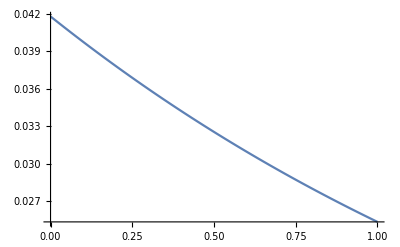

```mathematica
plotcomphase[3,0, 1,1.1,1,1.1,1]
```

And compare with the dynamics of each anomalous phase.

```mathematica
dottheta0[omega0_,Omega_, dom_,A01_,B01_,theta0_,theta1_] := (omega0^2 - Omega^2)/(2*Omega)*dom+A01*Sin[theta1-theta0] + 2B01*Sin[2*(theta1-theta0)]
```

```mathematica
dottheta1[omega1_,Omega_, dom_,A10_,B10_,theta0_,theta1_] := (omega1^2 - Omega^2)/(2*Omega)*dom-A10*Sin[theta1-theta0] - 2B10*Sin[2*(theta1-theta0)]
```

```mathematica
thetasoln[theta00_,theta10_,omega0_,omega1_,Omega_,dom_,A01_,A10_,B01_,B10_]:=NDSolve[{θ0'[t]== dottheta0[omega0,Omega,dom,A01,B01, θ0[t], θ1[t]], θ1'[t]== dottheta1[omega1,Omega,dom,A10,B10, θ0[t], θ1[t]],θ0[0]==theta00,θ1[0] == theta10},{θ0,θ1},{t, 0, 20}]
```

```mathematica
plottheta[theta00_,theta10_, omega0_, omega1_, Omega_,dom_,A01_,A10_,B01_,B10_,tf_]:= Plot[{Evaluate[θ0[t]/. thetasoln[theta00,theta10, omega0, omega1, Omega,dom,A01,A10,B01,B10]], Evaluate[θ1[t]/. thetasoln[theta00,theta10, omega0, omega1, Omega,dom,A01,A10,B01,B10]]},{t,0,tf},PlotRange->All]
```

```mathematica
Manipulate[plottheta[θ00,θ10,ω0, ω1,Ω,δ,A01,A10,B01,B10,5],{θ00,0,2π},{θ10,0, 2π},{ω0,0,10},{ω1,0,10},{Ω,0,10},{δ,0,1,1},{A01,0,15},{A10,0,15},{B01,0,15},{B10,0,15}]
```

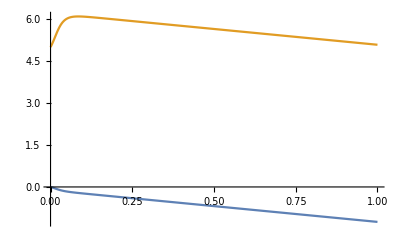

```mathematica
plottheta[0,5,2, 5,3.808,1,1,10,1,10,1]
```

Compare asymmetric coupling with symmetric coupling. 3.808

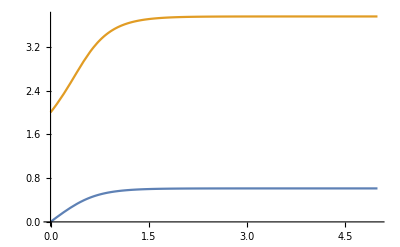

```mathematica
plottheta[0,2, 0, 0, 1,0,1,0,0,1,5]
```

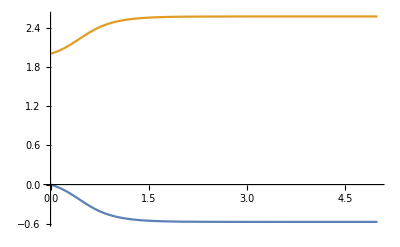

```mathematica
plottheta[0,2, 0, 0, 1,0,.5,.5,.5,.5,5]
```

Now compare this with the relative phase, which lacks information about the asymmetric coupling.

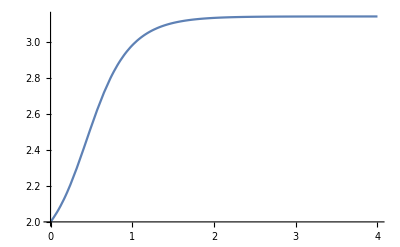

```mathematica
plotrelphase[2,0, 1,0,0,1,4]
```

```mathematica
plotrelphase[2,0, 0.5,0.5,0.5,0.5,4]
```

-Graphics-

Let’s try to come up with a potential function for the case of asymmetric coupling.

```mathematica
V[phi_]:={-(A10-A01)*Cos[phi]-(B10-B01)*Cos[phi],-(A10+A01)*Cos[Phi]-(B10+B01)*Cos[2*phi]}
```

```mathematica
Manipulate[ParametricPlot[{-(A10-A01)*Cos[phi]-(B10-B01)*Cos[phi],-(A10+A01)*Cos[Phi]-(B10+B01)*Cos[2*phi]},{phi,-4,5}],{A01,0,10},{A10,0,10},{B01,0,10},{B10,0,10}]
```

### Analysis of Center of Mass Phase Dynamics

Now, in the case of symmetric coupling when δΩ ≠ 0, the potential function becomes

V(Φ, ϕ) = -δΩ Φ - δω ϕ - 2A cos ϕ - 2B cos 2ϕ

This potential function is a rotated version of the potential for the anomalous phases.  In the original coordinates,
This has the effect of tilting the potential function in the Φ direction.

V(θ_0, θ_1) = -(ω_0^2 - Ω^2)/(2Ω) θ_0 -(ω_1^2 - Ω^2)/(2Ω) θ_1 - A cos(θ_1 - θ_0) - B cos(θ_1 - θ_0)

which for δΩ = 0 achieves its maximally symmetric form

V(θ_0, θ_1) = -δω/2(θ_1 - θ_0) - A cos(θ_1 - θ_0) - B cos(θ_1 - θ_0)

Let’s write a function that produces a 3D surface plot of the potential landscape in this case, with manipulation to alter the system parameters.

```mathematica
Manipulate[Plot3D[-δΩ*Φ -δω*ϕ - A*Cos[ϕ]-B*Cos[2ϕ],{ϕ, -4, 5}, {Φ, -4, 5}],{δΩ, 0, 4}, {δω, 0, 4}, {A, 1, 6}, {B, 1, 6}]
```

And compare with the potential function in the original coordinates.

```mathematica
Manipulate[Plot3D[-(ω1^2-Ω^2)/(2Ω)*d*θ1 -(ω0^2-Ω^2)/(2Ω)*d*θ0 - A*Cos[θ1-θ0]-B*Cos[2*(θ1-θ0)],{θ0, -4, 5}, {θ1, -4, 5}],{ω0, 0, 4}, {ω1, 0, 4}, {d,0,1,1},{Ω,1,4},{A, 0, 6}, {B, 0, 6}]
```

```mathematica
Manipulate[Plot3D[-(ω1^2-ω0^2)/(2ω0)*θ1  - A*Cos[θ1-θ0]-B*Cos[2*(θ1-θ0)],{θ0, -4, 5}, {θ1, -4, 5}],{ω0, 1, 10}, {ω1, 1, 10},{A, 0, 6}, {B, 0, 6}]
```

```mathematica
Manipulate[Plot3D[-(A10+A01)*Cos[θ1-θ0]-(B10+B01)*Cos[2*(θ1-θ0)],{θ0, -4, 5}, {θ1, -4, 5}],{A10,0,10},{A01,0,10},{B10, 0, 10}, {B01, 0, 10}]
```

```mathematica
Manipulate[Plot3D[-(A10-A01)*Cos[θ1-θ0]-(B10-B01)*Cos[2*(θ1-θ0)],{θ0, -4, 5}, {θ1, -4, 5}],{A10,0,10},{A01,0,10},{B10, 0, 10}, {B01, 0, 10}]
```

## Analysis of N + 1 = 3 Oscillators

With the generalization to higher dimensions, new possibilities for complex coordination emerge.  We will explore some of these.

### Third-Party Induced Bistability

Consider the fully symmetric case of N + 1 = 3 HKB oscillators.  Then the system’s dynamics can be derived from a potential function of the form

V(ϕ_1, ϕ_2) = - A_10 cos ϕ_1 - A_20 cos ϕ_2 - A_12 cos (ϕ_1 - ϕ_2) - B_10 cos ϕ_1 - B_20 cos ϕ_2 - B_12 cos (ϕ_1 - ϕ_2)

Now, we know from the case of N + 1 = 2 oscillators that for an isolated pair of oscillators i and j, the anti-phase attractor loses stability when   k_ij =B_ij/A_ij < 1/4   as a result of the dynamical landscape undergoing a bifurcation and destroying the anti-phase attractor basin.  
But now with N + 1 = 3 oscillators, we can have oscillators 1 and 2 coordinate anti-phase even when k_12 < 1/4 , making their coordination dynamics more complex than they would be in isolation from oscillator 0, and hence we say that the third-party oscillator 0 has induced bistability to the (1, 2)-pair.

This phenomenon of induced bistability can be seen most easily with the potential function.  Here, we generalize the potential function from the N + 1 = 2 oscillator case, with dials for manipulating the system’s coupling parameters (A_10, A_20, A_12, B_10, B_20, B_12).

```mathematica
Manipulate[Plot3D[- Subscript[A, 10]*Cos[Subscript[ϕ, 1]]-Subscript[A, 20]*Cos[Subscript[ϕ, 2]] - Subscript[A, 12]*Cos[Subscript[ϕ, 1]-Subscript[ϕ, 2]]-Subscript[B, 10]*Cos[2 Subscript[ϕ, 1]] -Subscript[B, 20]*Cos[2 Subscript[ϕ, 2]] - Subscript[B, 12]*Cos[2*(Subscript[ϕ, 1]-Subscript[ϕ, 2])],{Subscript[ϕ, 1], -4, 5}, {Subscript[ϕ, 2], -4, 5}],{Subscript[A, 10], 0, 10}, {Subscript[A, 20], 0, 10}, {Subscript[A, 12], 0, 10}, {Subscript[B, 10], 0, 10}, {Subscript[B, 20], 0, 10}, {Subscript[B, 12], 0, 10}]
```

This won’t rotate properly.  Try this.

```mathematica
plot = Manipulate[Graphics3D[Rotate[#,d*Degree,{0,0,1}],PlotRange->All,##2]&@@Plot3D[- A10*Cos[ϕ1]-A20*Cos[ϕ2] - A12*Cos[ϕ1-ϕ2]-B10*Cos[2ϕ1] -B20*Cos[2ϕ2] - B12*Cos[2*(ϕ1-ϕ2)],{ϕ1, -4, 5}, {ϕ2, -4, 5}],{A10, 0, 10}, {A20, 0, 10}, {A12, 0, 10}, {B10, 0, 10}, {B20, 0, 10}, {B12, 0, 10}]
```

Also, make a contour plot.

```mathematica
Manipulate[ContourPlot[- A10*Cos[ϕ1]-A20*Cos[ϕ2] - A12*Cos[ϕ1-ϕ2]-B10*Cos[2ϕ1] -B20*Cos[2ϕ2] - B12*Cos[2*(ϕ1-ϕ2)],{ϕ1,-4,5},{ϕ2,-4,5}],{A10, 0, 10}, {A20, 0, 10}, {A12, 0, 10}, {B10, 0, 10}, {B20, 0, 10}, {B12, 0, 10}]
```

```mathematica
ContourPlot[-Cos[ϕ1]-Cos[ϕ2] - 5*Cos[ϕ1-ϕ2]-20*Cos[2ϕ1] -20*Cos[2ϕ2] -Cos[2*(ϕ1-ϕ2)],{ϕ1,-4,5},{ϕ2,-4,5}]
```

-Graphics-

We can see that the anti-phase attractors between oscillators 1 and 2 are rescued by the third-party oscillator 0.

### Third-Party Pacing in Nonidentical Oscillators

The potential function for three oscillators can be generalized to describe the dynamics of nonidentical oscillators who differ in their eigenfrequencies.  In this case, the potential function becomes

```mathematica
V(Subscript[ϕ, 1], Subscript[ϕ, 2]) = -(Subscript[ω, 1]^2-Subscript[ω, rms]^2)/(2Ω)Subscript[ϕ, 1]-(Subscript[ω, 0]^2 - Subscript[ω, rms]^2)/(2Ω)Subscript[ϕ, 2]- Subscript[A, 10] cos Subscript[ϕ, 1] - Subscript[A, 20] cos Subscript[ϕ, 2] - Subscript[A, 12] cos (Subscript[ϕ, 1] - Subscript[ϕ, 2]) - Subscript[B, 10] cos Subscript[ϕ, 1] - Subscript[B, 20] cos Subscript[ϕ, 2] - Subscript[B, 12] cos (Subscript[ϕ, 1] - Subscript[ϕ, 2])
```

Now, for a given pair of oscillators 1 and 2 whose frequency difference is greater than δω_anti12^crit, the oscillator pair in isolation is only monostable since the frequency difference has annihilated the anti-phase attractor.  However, by coupling this pair to a third oscillator 0 of intermediate frequency, it is possible to restore bistability to the 1,2 pair.  We call this phenomenon third-party-pacing.

Because of the presence of ω_rms in the coefficients of ϕ_1 and ϕ_2, one can show that the frequency for the third-party oscillator 0 which maximizes the symmetry of the potential function, and hence the stability of all the fixed points, is given by

ω_0 = ω_rms(ω_1, ω_2) = √(1/2(ω_1^2 + ω_2^2))

which when δΩ = 0 means that oscillator 0 matches its frequency to the collective entrainment frequency oscillators 1 and 2 come to when isolated from oscillator 0.

Let’s produce a plot of the potential function for nonidentical oscillators.

```mathematica
plot = Manipulate[Graphics3D[Rotate[#,d*Degree,{0,0,1}],PlotRange->All,##2]&@@Plot3D[-(ω1^2 -1/3(ω0^2 + ω1^2 + ω2^2))/(2Ω)*ϕ1*dom -(ω2^2 -1/3(ω0^2 + ω1^2 + ω2^2))/(2Ω)*ϕ2*dom - A10*Cos[ϕ1]-A20*Cos[ϕ2] - A12*Cos[ϕ1-ϕ2]-B10*Cos[2ϕ1] -B20*Cos[2ϕ2] - B12*Cos[2*(ϕ1-ϕ2)],{ϕ1, -4, 5}, {ϕ2, -4, 5}],{d, 0, 180}, {dom,0,1,1},{ω0,0,10},{ω1,0,10},{ω2,0,10},{Ω,0,10},{A10, 0, 10}, {A20, 0, 10}, {A12, 0, 10}, {B10, 0, 10}, {B20, 0, 10}, {B12, 0, 10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Also make a contour plot.

```mathematica
Manipulate[ContourPlot[-(ω1^2 -1/3(ω0^2 + ω1^2 + ω2^2))/(2Ω)*ϕ1*dom -(ω2^2 -1/3(ω0^2 + ω1^2 + ω2^2))/(2Ω)*ϕ2*dom - A10*Cos[ϕ1]-A20*Cos[ϕ2] - A12*Cos[ϕ1-ϕ2]-B10*Cos[2ϕ1] -B20*Cos[2ϕ2] - B12*Cos[2*(ϕ1-ϕ2)],{ϕ1, -4, 5}, {ϕ2, -4, 5}],{d, 0, 180}, {dom,0,1,1},{ω0,0,10},{ω1,0,10},{ω2,0,10},{Ω,0,10},{A10, 0, 10}, {A20, 0, 10}, {A12, 0, 10}, {B10, 0, 10}, {B20, 0, 10}, {B12, 0, 10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

We see that setting Ω = ω_0 = ω_rms maximizes the stability of the potential landscape.

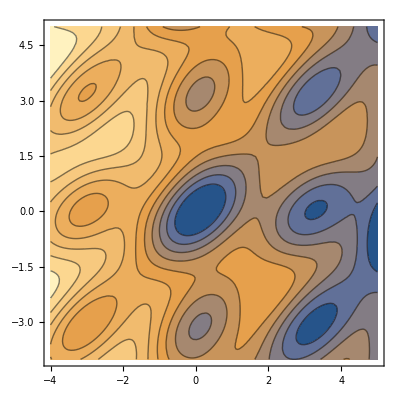

```mathematica
ContourPlot[-(49 -1/3(25))/50*ϕ1 -(1 -1/3(25))/50*ϕ2 - Cos[ϕ1]-Cos[ϕ2] - Cos[ϕ1-ϕ2]-Cos[2ϕ1] -Cos[2ϕ2] - Cos[2*(ϕ1-ϕ2)],{ϕ1, -4, 5}, {ϕ2, -4, 5}, Contours -> 10]
```

### Asymmetric Coupling and Anomalous Phase Oscillations

For asymmetric coupling, it is no longer possible to represent the system’s dynamics with a potential function.  So, to best gain insight into this system we should do simulations.  We will simulate the general anomalous phase equations for three oscillators.

```mathematica
dottheta0[omega0_,Omega_, dom_,A01_,A02_,B01_,B02_,theta0_,theta1_,theta2_] := (omega0^2 - Omega^2)/(2*Omega)*dom+A01*Sin[theta1-theta0] + A02*Sin[theta2-theta0]+2B01*Sin[2*(theta1-theta0)] + 2B02*Sin[2*(theta2-theta0)]
```

```mathematica
dottheta1[omega1_,Omega_, dom_,A10_,A12_,B10_,B12_,theta0_,theta1_,theta2_] := (omega1^2 - Omega^2)/(2*Omega)*dom-A10*Sin[theta1-theta0] - A12*Sin[theta1-theta2]+2B10*Sin[2*(theta1-theta0)] + 2B12*Sin[2*(theta1-theta2)]
```

```mathematica
dottheta2[omega2_,Omega_, dom_,A20_,A21_,B20_,B21_,theta0_,theta1_,theta2_] := (omega2^2 - Omega^2)/(2*Omega)*dom-A20*Sin[theta2-theta0] + A21*Sin[theta1-theta2]-2B20*Sin[2*(theta2-theta0)] + 2B21*Sin[2*(theta1-theta2)]
```

```mathematica
thetasoln3[1,1,2,1,1,2,1,1,1,0.1,1,0.1,1,0.1,1,0.1,1,0.1,1,0.1]
```

{{θ0→InterpolatingFunction[…],θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]}}

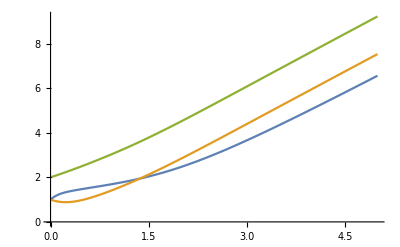

```mathematica
plottheta3[1,1,2,1,1,2,1,1,1,0.1,1,0.1,1,0.1,1,0.1,1,0.1,1,0.1,5]
```

```mathematica
thetasoln3[theta00_,theta10_,theta20_,omega0_,omega1_,omega2_,Omega_,dom_,A01_,A10_,A02_,A20_,A12_,A21_,B01_,B10_,B02_,B20_,B12_,B21_]:=NDSolve[{θ0'[t]== dottheta0[omega0,Omega, dom,A01,A02,B01,B02,θ0[t],θ1[t],θ2[t]], θ1'[t]== dottheta1[omega1,Omega, dom,A10,A12,B10,B12,θ0[t],θ1[t],θ2[t]],θ2'[t]==dottheta2[omega2,Omega, dom,A20,A21,B20,B21,θ0[t],θ1[t],θ2[t]],θ0[0]==theta00,θ1[0] == theta10, θ2[0]==theta20},{θ0,θ1,θ2},{t, 0, 100}]
```

```mathematica
plottheta3[theta00_,theta10_,theta20_,omega0_,omega1_,omega2_,Omega_,dom_,A01_,A10_,A02_,A20_,A12_,A21_,B01_,B10_,B02_,B20_,B12_,B21_,tf_]:= Plot[{Evaluate[θ0[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]], Evaluate[θ1[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]],Evaluate[θ2[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]},{t,0,tf},PlotRange->All]
```

```mathematica
Manipulate[plottheta3[θ00,θ10,θ20,ω0, ω1,ω2,Ω,δ,A01,A10,A02,A20,A12,A21,B01,B10, B02,B20,B12,B21,10],{θ00,0,2π},{θ10,0, 2π},{θ20,0,2π},{ω0,0,10},{ω1,0,10},{ω2,0,10},{Ω,0,10},{δ,0,1,1},{A01,0,15},{A10,0,15},{A02,0,15},{A20,0,15},{A12,0,15},{A21,0,15},{B01,0,15},{B10,0,15},{B02,0,15},{B20,0,15},{B12,0,15},{B21,0,15}]
```

With 12 different coupling parameters, there’s bound to be some kind of new, interesting dynamics afforded by the asymmetric coupling.  Let’s try random settings and see if we can make anything interesting.

We get wavelike patterns from asymmetric coupling when θ(0) = (0,3.568,1.85982) and A=(0,0.7,4.96,0.04,0.72,0.56) and B = (0.38, 0.28, 0.58, 4.3, 0, 3.5).

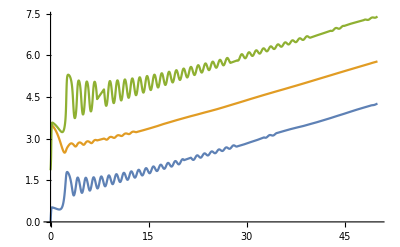

```mathematica
plottheta3[0,3.568,1.85982,0,0,0,1,0,0,0.7,4.96,0.04,0.72,0.56,0.38,0.28,0.58,4.3,0,3.5,50]
```

Now let’s plot the relative phases and the center of mass phase.

```mathematica
plotphi3[theta00_,theta10_,theta20_,omega0_,omega1_,omega2_,Omega_,dom_,A01_,A10_,A02_,A20_,A12_,A21_,B01_,B10_,B02_,B20_,B12_,B21_,tf_]:= Plot[{Evaluate[θ1[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]-Evaluate[θ0[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]], Evaluate[θ2[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]-Evaluate[θ0[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]],Evaluate[θ0[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]+Evaluate[θ1[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]+Evaluate[θ2[t]/. thetasoln3[theta00,theta10,theta20,omega0,omega1,omega2,Omega,dom,A01,A10,A02,A20,A12,A21,B01,B10,B02,B20,B12,B21]]},{t,0,tf},PlotRange->All]
```

```mathematica
Manipulate[plotphi3[θ00,θ10,θ20,ω0, ω1,ω2,Ω,δ,A01,A10,A02,A20,A12,A21,B01,B10, B02,B20,B12,B21,10],{θ00,0,2π},{θ10,0, 2π},{θ20,0,2π},{ω0,0,10},{ω1,0,10},{ω2,0,10},{Ω,0,10},{δ,0,1,1},{A01,0,15},{A10,0,15},{A02,0,15},{A20,0,15},{A12,0,15},{A21,0,15},{B01,0,15},{B10,0,15},{B02,0,15},{B20,0,15},{B12,0,15},{B21,0,15}]
```

ReplaceAll::reps: {NDSolve[{θ0'[0.000204286]==Indeterminate,θ1'[0.000204286]==Indeterminate,θ2'[0.000204286]==Indeterminate,θ0[0]==0,θ1[0]==0,θ2[0]==0},{θ0,θ1,θ2},{0.000204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{θ0'[0.000204286]==Indeterminate,θ1'[0.000204286]==Indeterminate,θ2'[0.000204286]==Indeterminate,θ0[0]==0,θ1[0]==0,θ2[0]==0},{θ0,θ1,θ2},{0.000204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

ReplaceAll::reps: {NDSolve[{θ0'[0.000204286]==Indeterminate,θ1'[0.000204286]==Indeterminate,θ2'[0.000204286]==Indeterminate,θ0[0]==0,θ1[0]==0,θ2[0]==0},{θ0,θ1,θ2},{0.000204286,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Lyapunov Functions

```mathematica
dVd0 = -(A10+A01)*Sin[phi1]-(A20+A02)*Sin[phi2]-2*(B10+B01)*Sin[2*phi1]-2*(B20+B02)*Sin[2*phi2]
```

(-A01-A10) Sin[phi1]-2 (B01+B10) Sin[2 phi1]-(A02+A20) Sin[phi2]-2 (B02+B20) Sin[2 phi2]

```mathematica
dVd1 = (A10+A01)*Sin[phi1]+(A12+A21)*Sin[phi1-phi2]+2*(B10+B01)*Sin[2*phi1]+2*(B12+B21)*Sin[2*(phi1-phi2)]
```

(A01+A10) Sin[phi1]+2 (B01+B10) Sin[2 phi1]+(A12+A21) Sin[phi1-phi2]+2 (B12+B21) Sin[2 (phi1-phi2)]

```mathematica
dVd2 = (A20+A02)*Sin[phi2]-(A12+A21)*Sin[phi1-phi2]+2*(B20+B02)*Sin[2*phi2]-2*(B12+B21)*Sin[2*(phi1-phi2)]
```

-((A12+A21) Sin[phi1-phi2])-2 (B12+B21) Sin[2 (phi1-phi2)]+(A02+A20) Sin[phi2]+2 (B02+B20) Sin[2 phi2]

```mathematica
dot0 = A01*Sin[phi1]+A02*Sin[phi2]+2*B01*Sin[2*phi1]+2*B02*Sin[2*phi2]
```

A01 Sin[phi1]+2 B01 Sin[2 phi1]+A02 Sin[phi2]+2 B02 Sin[2 phi2]

```mathematica
dot1 = -A10*Sin[phi1]-A12*Sin[phi1-phi2]-2*B10*Sin[2*phi1]-2*B12*Sin[2*(phi1-phi2)]
```

-A10 Sin[phi1]-2 B10 Sin[2 phi1]-A12 Sin[phi1-phi2]-2 B12 Sin[2 (phi1-phi2)]

```mathematica
dot2 = -A20*Sin[phi2]+A21*Sin[phi1-phi2]-2*B20*Sin[2*phi2]+2*B21*Sin[2*(phi1-phi2)]
```

A21 Sin[phi1-phi2]+2 B21 Sin[2 (phi1-phi2)]-A20 Sin[phi2]-2 B20 Sin[2 phi2]

```mathematica
dotV = dVd0*dot0+dVd1*dot1+dVd2*dot2
```

(-A10 Sin[phi1]-2 B10 Sin[2 phi1]-A12 Sin[phi1-phi2]-2 B12 Sin[2 (phi1-phi2)]) ((A01+A10) Sin[phi1]+2 (B01+B10) Sin[2 phi1]+(A12+A21) Sin[phi1-phi2]+2 (B12+B21) Sin[2 (phi1-phi2)])+(A01 Sin[phi1]+2 B01 Sin[2 phi1]+A02 Sin[phi2]+2 B02 Sin[2 phi2]) ((-A01-A10) Sin[phi1]-2 (B01+B10) Sin[2 phi1]-(A02+A20) Sin[phi2]-2 (B02+B20) Sin[2 phi2])+(A21 Sin[phi1-phi2]+2 B21 Sin[2 (phi1-phi2)]-A20 Sin[phi2]-2 B20 Sin[2 phi2]) (-((A12+A21) Sin[phi1-phi2])-2 (B12+B21) Sin[2 (phi1-phi2)]+(A02+A20) Sin[phi2]+2 (B02+B20) Sin[2 phi2])

```mathematica
Expand[dotV]
```

-A01^2 Sin[phi1]^2-2 A01 A10 Sin[phi1]^2-A10^2 Sin[phi1]^2-4 A01 B01 Sin[phi1] Sin[2 phi1]-4 A10 B01 Sin[phi1] Sin[2 phi1]-4 A01 B10 Sin[phi1] Sin[2 phi1]-4 A10 B10 Sin[phi1] Sin[2 phi1]-4 B01^2 Sin[2 phi1]^2-8 B01 B10 Sin[2 phi1]^2-4 B10^2 Sin[2 phi1]^2-A01 A12 Sin[phi1] Sin[phi1-phi2]-2 A10 A12 Sin[phi1] Sin[phi1-phi2]-A10 A21 Sin[phi1] Sin[phi1-phi2]-2 A12 B01 Sin[2 phi1] Sin[phi1-phi2]-4 A12 B10 Sin[2 phi1] Sin[phi1-phi2]-2 A21 B10 Sin[2 phi1] Sin[phi1-phi2]-A12^2 Sin[phi1-phi2]^2-2 A12 A21 Sin[phi1-phi2]^2-A21^2 Sin[phi1-phi2]^2-2 A01 B12 Sin[phi1] Sin[2 (phi1-phi2)]-4 A10 B12 Sin[phi1] Sin[2 (phi1-phi2)]-2 A10 B21 Sin[phi1] Sin[2 (phi1-phi2)]-4 B01 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-8 B10 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-4 B10 B21 Sin[2 phi1] Sin[2 (phi1-phi2)]-4 A12 B12 Sin[phi1-phi2] Sin[2 (phi1-phi2)]-4 A21 B12 Sin[phi1-phi2] Sin[2 (phi1-phi2)]-4 A12 B21 Sin[phi1-phi2] Sin[2 (phi1-phi2)]-4 A21 B21 Sin[phi1-phi2] Sin[2 (phi1-phi2)]-4 B12^2 Sin[2 (phi1-phi2)]^2-8 B12 B21 Sin[2 (phi1-phi2)]^2-4 B21^2 Sin[2 (phi1-phi2)]^2-2 A01 A02 Sin[phi1] Sin[phi2]-A02 A10 Sin[phi1] Sin[phi2]-A01 A20 Sin[phi1] Sin[phi2]-4 A02 B01 Sin[2 phi1] Sin[phi2]-2 A20 B01 Sin[2 phi1] Sin[phi2]-2 A02 B10 Sin[2 phi1] Sin[phi2]+A12 A20 Sin[phi1-phi2] Sin[phi2]+A02 A21 Sin[phi1-phi2] Sin[phi2]+2 A20 A21 Sin[phi1-phi2] Sin[phi2]+2 A20 B12 Sin[2 (phi1-phi2)] Sin[phi2]+2 A02 B21 Sin[2 (phi1-phi2)] Sin[phi2]+4 A20 B21 Sin[2 (phi1-phi2)] Sin[phi2]-A02^2 Sin[phi2]^2-2 A02 A20 Sin[phi2]^2-A20^2 Sin[phi2]^2-4 A01 B02 Sin[phi1] Sin[2 phi2]-2 A10 B02 Sin[phi1] Sin[2 phi2]-2 A01 B20 Sin[phi1] Sin[2 phi2]-8 B01 B02 Sin[2 phi1] Sin[2 phi2]-4 B02 B10 Sin[2 phi1] Sin[2 phi2]-4 B01 B20 Sin[2 phi1] Sin[2 phi2]+2 A21 B02 Sin[phi1-phi2] Sin[2 phi2]+2 A12 B20 Sin[phi1-phi2] Sin[2 phi2]+4 A21 B20 Sin[phi1-phi2] Sin[2 phi2]+4 B12 B20 Sin[2 (phi1-phi2)] Sin[2 phi2]+4 B02 B21 Sin[2 (phi1-phi2)] Sin[2 phi2]+8 B20 B21 Sin[2 (phi1-phi2)] Sin[2 phi2]-4 A02 B02 Sin[phi2] Sin[2 phi2]-4 A20 B02 Sin[phi2] Sin[2 phi2]-4 A02 B20 Sin[phi2] Sin[2 phi2]-4 A20 B20 Sin[phi2] Sin[2 phi2]-4 B02^2 Sin[2 phi2]^2-8 B02 B20 Sin[2 phi2]^2-4 B20^2 Sin[2 phi2]^2

```mathematica
guess = Expand[(-(A10+A01)*Sin[phi1]-(A20+A02)*Sin[phi2]+(A12+A21)*Sin[phi1-phi2]- 2*(B10+B01)*Sin[2*phi1]-2*(B20+B02)*Sin[2*phi2]+2*(B12+B21)*Sin[2*(phi1-phi2)])^2]
```

A01^2 Sin[phi1]^2+2 A01 A10 Sin[phi1]^2+A10^2 Sin[phi1]^2+4 A01 B01 Sin[phi1] Sin[2 phi1]+4 A10 B01 Sin[phi1] Sin[2 phi1]+4 A01 B10 Sin[phi1] Sin[2 phi1]+4 A10 B10 Sin[phi1] Sin[2 phi1]+4 B01^2 Sin[2 phi1]^2+8 B01 B10 Sin[2 phi1]^2+4 B10^2 Sin[2 phi1]^2-2 A01 A12 Sin[phi1] Sin[phi1-phi2]-2 A10 A12 Sin[phi1] Sin[phi1-phi2]-2 A01 A21 Sin[phi1] Sin[phi1-phi2]-2 A10 A21 Sin[phi1] Sin[phi1-phi2]-4 A12 B01 Sin[2 phi1] Sin[phi1-phi2]-4 A21 B01 Sin[2 phi1] Sin[phi1-phi2]-4 A12 B10 Sin[2 phi1] Sin[phi1-phi2]-4 A21 B10 Sin[2 phi1] Sin[phi1-phi2]+A12^2 Sin[phi1-phi2]^2+2 A12 A21 Sin[phi1-phi2]^2+A21^2 Sin[phi1-phi2]^2-4 A01 B12 Sin[phi1] Sin[2 (phi1-phi2)]-4 A10 B12 Sin[phi1] Sin[2 (phi1-phi2)]-4 A01 B21 Sin[phi1] Sin[2 (phi1-phi2)]-4 A10 B21 Sin[phi1] Sin[2 (phi1-phi2)]-8 B01 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-8 B10 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-8 B01 B21 Sin[2 phi1] Sin[2 (phi1-phi2)]-8 B10 B21 Sin[2 phi1] Sin[2 (phi1-phi2)]+4 A12 B12 Sin[phi1-phi2] Sin[2 (phi1-phi2)]+4 A21 B12 Sin[phi1-phi2] Sin[2 (phi1-phi2)]+4 A12 B21 Sin[phi1-phi2] Sin[2 (phi1-phi2)]+4 A21 B21 Sin[phi1-phi2] Sin[2 (phi1-phi2)]+4 B12^2 Sin[2 (phi1-phi2)]^2+8 B12 B21 Sin[2 (phi1-phi2)]^2+4 B21^2 Sin[2 (phi1-phi2)]^2+2 A01 A02 Sin[phi1] Sin[phi2]+2 A02 A10 Sin[phi1] Sin[phi2]+2 A01 A20 Sin[phi1] Sin[phi2]+2 A10 A20 Sin[phi1] Sin[phi2]+4 A02 B01 Sin[2 phi1] Sin[phi2]+4 A20 B01 Sin[2 phi1] Sin[phi2]+4 A02 B10 Sin[2 phi1] Sin[phi2]+4 A20 B10 Sin[2 phi1] Sin[phi2]-2 A02 A12 Sin[phi1-phi2] Sin[phi2]-2 A12 A20 Sin[phi1-phi2] Sin[phi2]-2 A02 A21 Sin[phi1-phi2] Sin[phi2]-2 A20 A21 Sin[phi1-phi2] Sin[phi2]-4 A02 B12 Sin[2 (phi1-phi2)] Sin[phi2]-4 A20 B12 Sin[2 (phi1-phi2)] Sin[phi2]-4 A02 B21 Sin[2 (phi1-phi2)] Sin[phi2]-4 A20 B21 Sin[2 (phi1-phi2)] Sin[phi2]+A02^2 Sin[phi2]^2+2 A02 A20 Sin[phi2]^2+A20^2 Sin[phi2]^2+4 A01 B02 Sin[phi1] Sin[2 phi2]+4 A10 B02 Sin[phi1] Sin[2 phi2]+4 A01 B20 Sin[phi1] Sin[2 phi2]+4 A10 B20 Sin[phi1] Sin[2 phi2]+8 B01 B02 Sin[2 phi1] Sin[2 phi2]+8 B02 B10 Sin[2 phi1] Sin[2 phi2]+8 B01 B20 Sin[2 phi1] Sin[2 phi2]+8 B10 B20 Sin[2 phi1] Sin[2 phi2]-4 A12 B02 Sin[phi1-phi2] Sin[2 phi2]-4 A21 B02 Sin[phi1-phi2] Sin[2 phi2]-4 A12 B20 Sin[phi1-phi2] Sin[2 phi2]-4 A21 B20 Sin[phi1-phi2] Sin[2 phi2]-8 B02 B12 Sin[2 (phi1-phi2)] Sin[2 phi2]-8 B12 B20 Sin[2 (phi1-phi2)] Sin[2 phi2]-8 B02 B21 Sin[2 (phi1-phi2)] Sin[2 phi2]-8 B20 B21 Sin[2 (phi1-phi2)] Sin[2 phi2]+4 A02 B02 Sin[phi2] Sin[2 phi2]+4 A20 B02 Sin[phi2] Sin[2 phi2]+4 A02 B20 Sin[phi2] Sin[2 phi2]+4 A20 B20 Sin[phi2] Sin[2 phi2]+4 B02^2 Sin[2 phi2]^2+8 B02 B20 Sin[2 phi2]^2+4 B20^2 Sin[2 phi2]^2

```mathematica
Expand[dotV]+guess
```

-3 A01 A12 Sin[phi1] Sin[phi1-phi2]-4 A10 A12 Sin[phi1] Sin[phi1-phi2]-2 A01 A21 Sin[phi1] Sin[phi1-phi2]-3 A10 A21 Sin[phi1] Sin[phi1-phi2]-6 A12 B01 Sin[2 phi1] Sin[phi1-phi2]-4 A21 B01 Sin[2 phi1] Sin[phi1-phi2]-8 A12 B10 Sin[2 phi1] Sin[phi1-phi2]-6 A21 B10 Sin[2 phi1] Sin[phi1-phi2]-6 A01 B12 Sin[phi1] Sin[2 (phi1-phi2)]-8 A10 B12 Sin[phi1] Sin[2 (phi1-phi2)]-4 A01 B21 Sin[phi1] Sin[2 (phi1-phi2)]-6 A10 B21 Sin[phi1] Sin[2 (phi1-phi2)]-12 B01 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-16 B10 B12 Sin[2 phi1] Sin[2 (phi1-phi2)]-8 B01 B21 Sin[2 phi1] Sin[2 (phi1-phi2)]-12 B10 B21 Sin[2 phi1] Sin[2 (phi1-phi2)]+A02 A10 Sin[phi1] Sin[phi2]+A01 A20 Sin[phi1] Sin[phi2]+2 A10 A20 Sin[phi1] Sin[phi2]+2 A20 B01 Sin[2 phi1] Sin[phi2]+2 A02 B10 Sin[2 phi1] Sin[phi2]+4 A20 B10 Sin[2 phi1] Sin[phi2]-2 A02 A12 Sin[phi1-phi2] Sin[phi2]-A12 A20 Sin[phi1-phi2] Sin[phi2]-A02 A21 Sin[phi1-phi2] Sin[phi2]-4 A02 B12 Sin[2 (phi1-phi2)] Sin[phi2]-2 A20 B12 Sin[2 (phi1-phi2)] Sin[phi2]-2 A02 B21 Sin[2 (phi1-phi2)] Sin[phi2]+2 A10 B02 Sin[phi1] Sin[2 phi2]+2 A01 B20 Sin[phi1] Sin[2 phi2]+4 A10 B20 Sin[phi1] Sin[2 phi2]+4 B02 B10 Sin[2 phi1] Sin[2 phi2]+4 B01 B20 Sin[2 phi1] Sin[2 phi2]+8 B10 B20 Sin[2 phi1] Sin[2 phi2]-4 A12 B02 Sin[phi1-phi2] Sin[2 phi2]-2 A21 B02 Sin[phi1-phi2] Sin[2 phi2]-2 A12 B20 Sin[phi1-phi2] Sin[2 phi2]-8 B02 B12 Sin[2 (phi1-phi2)] Sin[2 phi2]-4 B12 B20 Sin[2 (phi1-phi2)] Sin[2 phi2]-4 B02 B21 Sin[2 (phi1-phi2)] Sin[2 phi2]

## Analysis of General Systems of N + 1 HKB Phase Oscillators

## Analysis of Systems with Variable Amplitudes

## Analysis of the General Rayleigh-van-der-Pol Equations

## References

Third Party Stabilization of Unstable Coordination in Systems of Coupled Oscillators
By Joseph McKinley et al.
https://iopscience.iop.org/article/10.1088/1742-6596/2090/1/012167/pdf